```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\GitHub\optics_R_exp\optics_data

```mathematica
opticsfitgraph[r0_]:=Module[{x,x1,y,y1,data,data1,p1,p2,f},
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data=Transpose[{x1,y1}];
data1=data⟦20;;⟧;
p1=ListPlot[data,PlotRange->All];
f=Normal[NonlinearModelFit[data,a+b ArcTan[c t+d],{a,b,c,d},t]];
p2=Plot[f,{t,0,1},PlotRange->All,PlotStyle->Red];
Show[p1,p2]
]
```

```mathematica
opticsfitf[r0_]:=Module[{x,x1,y,y1,data,data1,p1,p2,f},
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data=Transpose[{x1,y1}];
data1=data⟦20;;⟧;
f=Normal[NonlinearModelFit[data,a+b ArcTan[c t+d],{a,b,c,d},t]];
Return[f]
]
```

```mathematica
residualdata[r0_]:=Module[{x,x1,y,y1,data,data1,p1,p2,f},
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data=Transpose[{x1,y1}];
data1=data⟦20;;⟧;
f=Normal[NonlinearModelFit[data,a+b ArcTan[c t+d],{a,b,c,d},t]];
Return[Transpose[{x1,y1-Evaluate[f/.t->x1]}]]
]
```

```mathematica
dat=residualdata[0.2];
```

```mathematica
dat1=Transpose[{Transpose[dat]⟦1⟧,(Transpose[dat]⟦2⟧-Min[Transpose[dat]⟦2⟧])/Max[(Transpose[dat]⟦2⟧-Min[Transpose[dat]⟦2⟧])]}];
```

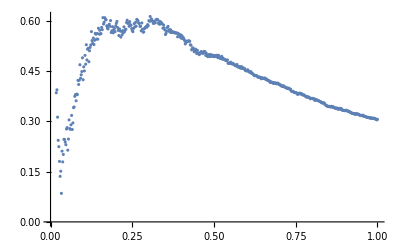

```mathematica
p1=ListPlot[dat1⟦10;;-1⟧]
```

```mathematica
parabola = Fit[dat1⟦10;;-1⟧, Table[t^n,{n,0,5}], t]
```

0.0577993+5.79985 t-22.0627 t^2+36.925 t^3-29.6223 t^4+9.21239 t^5

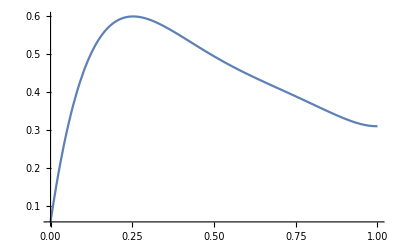

```mathematica
p2=Plot[parabola,{t,0,1}]
```

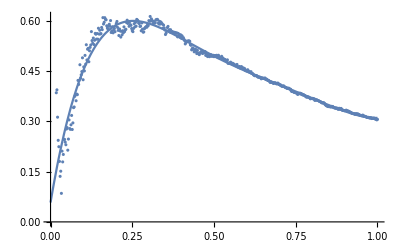

```mathematica
Show[p1,p2]
```

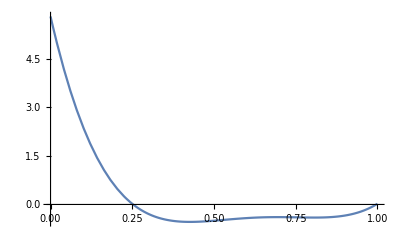

```mathematica
Plot[Evaluate[D[parabola,t]],{t,0,1},PlotRange->All]
```

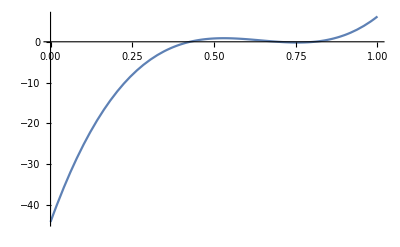

0

```mathematica
Plot[Evaluate[D[parabola,{t,2}]],{t,0,1}]
```

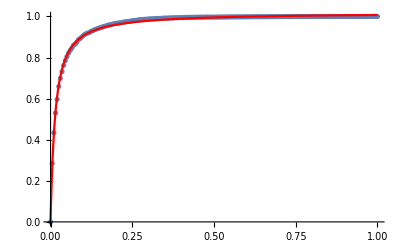

```mathematica
opticsfitgraph[0.1]
```

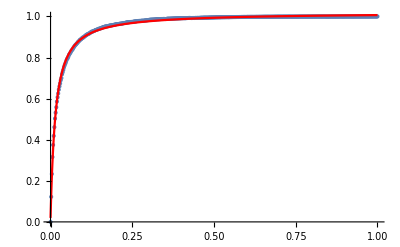

```mathematica
opticsfitgraph[0.2]
```

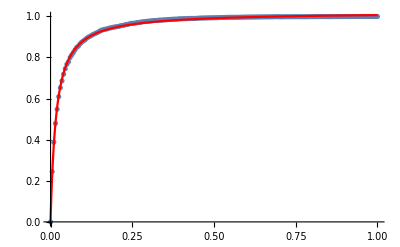

```mathematica
opticsfitgraph[0.3]
```

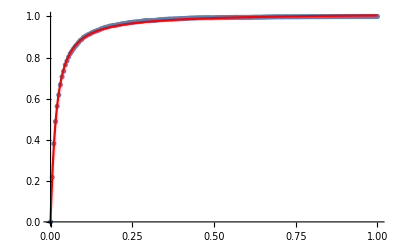

```mathematica
opticsfitgraph[0.4]
```

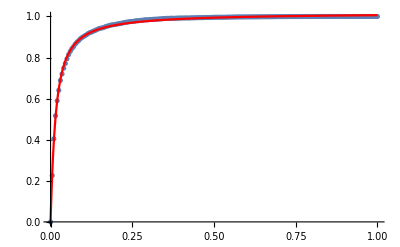

```mathematica
opticsfitgraph[0.5]
```

```mathematica
opticsfitf[0.1]
```

-0.793719+1.15432 ArcTan[0.830532+92.5333 t]

```mathematica
opticsfitf[0.2]
```

-0.978811+1.27245 ArcTan[0.998183+93.9141 t]

```mathematica
opticsfitf[0.3]
```

-1.16392+1.39158 ArcTan[1.11763+87.4481 t]

```mathematica
opticsfitf[0.35]
```

-0.329149+0.857431 ArcTan[0.414138+76.7356 t]

```mathematica
opticsfitf[0.4]
```

-0.311996+0.846795 ArcTan[0.389576+64.1595 t]

```mathematica
opticsfitf[0.5]
```

-0.382124+0.891551 ArcTan[0.455848+71.6835 t]

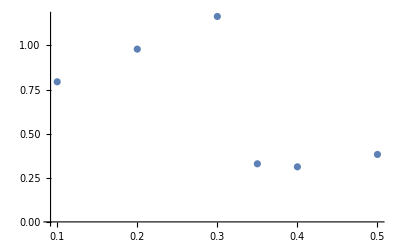

```mathematica
aplot=ListPlot[{{0.1,0.7937194475021443},{0.2,0.9788107928567081},{0.3,1.1639162856750962},{0.35,0.3291489894417684},{0.4,0.311995973905801},{0.5,0.38212367136490966}}]
```

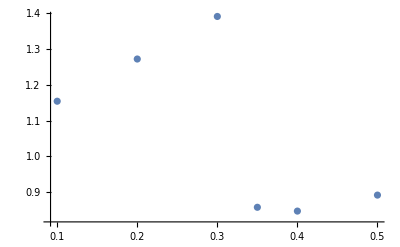

```mathematica
bplot=ListPlot[{{0.1,1.154319555817642},{0.2,1.272448875269659 },{0.3,1.3915808863805366 },{0.35, 0.8574312526258469 },{0.4,0.8467949168437876 },{0.5,0.8915505438463871}}]
```

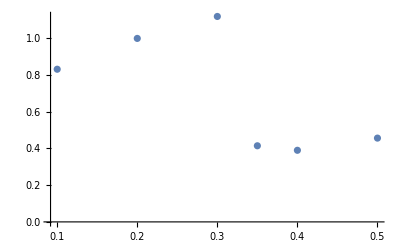

```mathematica
cplot=ListPlot[{{0.1,0.8305321157003214},{0.2,0.9981832737070772 },{0.3,1.117628405778848},{0.35,0.4141383346735879},{0.4,0.38957620182352765},{0.5,0.4558484222056781}}]
```

```mathematica
FindFormula[{{0.35,0.4141383346735879},{0.4,0.38957620182352765},{0.5,0.4558484222056781}},t]
```

1.66311-6.26107 Global`t+7.6931 (Global`t)^2

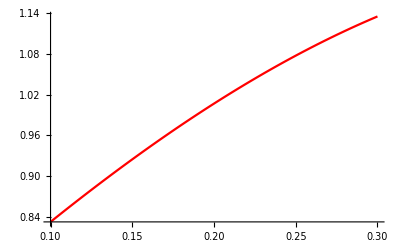

```mathematica
cplotf1=Plot[{0.6270841051442384+2.1435321296529772 t-2.7470575447677814 t^2.5},{t,0.1,0.3},PlotStyle->Red]
```

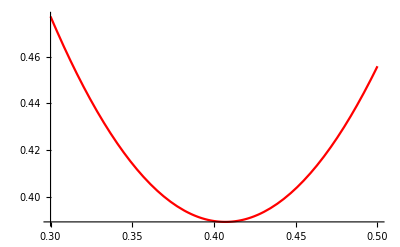

```mathematica
cplotf2=Plot[{1.66310713472706-6.26106696112356 t+7.6930990721616235 t^2},{t,0.3,0.5},PlotStyle->Red]
```

```mathematica
Show[cplot,cplotf1,cplotf2]
```

Show::gcomb: Could not combine the graphics objects in Show[cplot,,].

Show[cplot,-Graphics-,-Graphics-]

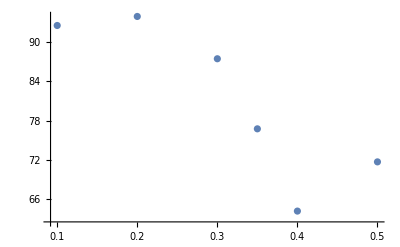

```mathematica
dplot=ListPlot[{{0.1,92.53331321275623},{0.2,93.91409616101483 },{0.3,87.44807107554114 },{0.35,76.73560902641815},{0.4,64.15946080453008 },{0.5,71.68350994957764}}]
```

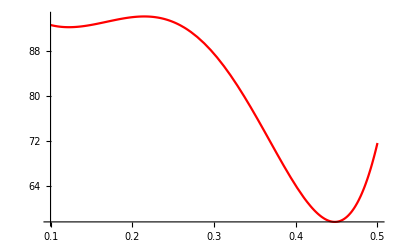

```mathematica
dplot1=Plot[107.9835588206598-278.35427810713514 t+1090.5808847614962 t^2+3893.2930526632795 t^3-27548.27716786023 t^4+34090.80193281391 t^5,{t,0.1,0.5},PlotStyle->Red]
```

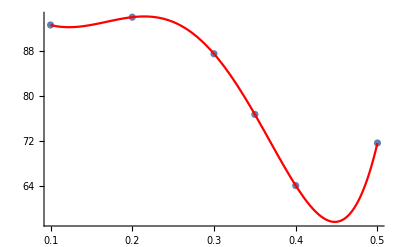

```mathematica
Show[dplot,dplot1,PlotRange->All]
```

```mathematica
FindFormula[{{0.1,92.53331321275623},{0.2,93.91409616101483 },{0.3,87.44807107554114 },{0.35,76.73560902641815},{0.4,64.15946080453008 },{0.5,71.68350994957764}},t]
```

107.984-278.354 t+1090.58 t^2+3893.29 t^3-27548.3 t^4+34090.8 t^5

WolframAlphaQueryResults